```mathematica
Clear/@{configurationAdd,configurationMinus,partial,hasEmptyIntersection,simplexes};


(*
This part contains the data of simplicial complex and the types of excitations.
*)
(*Whether you want to compute E/Subscript[E, id] and D/Subscript[D, id]*)
computeE=True;
computeD=True;
(* These are the types of excitations. You can set their dimensions separately*)
types=2;
n={2,2,2};
dim={1,1,2};
(*The data of simplicial complex is determined by the top-dimensional simplexes. It is a list of simplexes, every simplex is determined by its vertices.*)
topDimensionSimplexes={{1,2,3,4}};
(*If you want to compute localized statistics*)
doLocalization=False;
localizationRegion={1,2,3,4};

(*A technical parameter used in computing Smith decomposition. It do not change the result, but may affect the time cost.*)
compressThreshold=2.7;

(*
In this part, we generate some functions in need to compute statistics
*)

simplexes[-1]=={{}};(*There is one (-1)-dimensional simplex*)

(*The set of simplexes in every dimension. simplexes[p] is described by {s1,s2,...sn}, every si is a p-simplex, described by (p+1) vertices.*)
simplexes[dimension_]:=simplexes[dimension]=Union@@(Subsets[#,{dimension+1}]&/@topDimensionSimplexes);

(*A p-chain is described by a Association from simplexes[p] to Integer. The function chainBoundary gives the chain-level boundary with integer coefficient.*)
chainBoundary[chain_,dimension_]:=Module[{boundaryChain=AssociationThread[simplexes[dimension-1],0]},
Do[
Do[
boundaryChain[Delete[s,i]]+=(-1)^(i-1)*chain[s];
,{i,dimension+1}];
,{s,simplexes[dimension]}];
boundaryChain
];

(*A technical function*)
vectorDivision[a_,b_]:=LCM@@Table[If[#1==0&&#2!=0,0,If[#2==0,1,#1/GCD[#1,#2]]]&[a[[i]],b[[i]]],{i,Length[a]}];


(*We generate the group of all configurations and assign a integer in {1,2,...,dimH} to every configuration as its index*)
cycles=ConstantArray[{},types];
cyclesGenerators=ConstantArray[{},types];
Do[
chains=Association@@@(Thread[simplexes[dim[[type]]+1]->#]&/@Tuples[Range[0,n[[type]]-1],Length[simplexes[dim[[type]]+1]]]);
Do[If[!MemberQ[cycles[[type]],Mod[chainBoundary[chain,dim[[type]]+1],n[[type]]]],AppendTo[cycles[[type]],Mod[chainBoundary[chain,dim[[type]]+1],n[[type]]]];AppendTo[cyclesGenerators[[type]],Values[chain]];]
,{chain,chains}];
,{type,types}]
configurations=Tuples[cycles];
dimH=Length[configurations];
configurationsIndexMap=AssociationThread[configurations->Range[dimH]];

(*These two functions are only used in drawgraph[]*)
configurationGenerators=Flatten/@Tuples[cyclesGenerators];
configurationName[generators_]:=Module[{terms,mathExpr},terms=Table[If[generators[[i]]==1,Subscript["U",i],If[generators[[i]]!=0,Superscript[Subscript["U",i],generators[[i]]],Nothing]],{i,Length[generators]}];
mathExpr=Row[terms,""];
Framed[mathExpr]];

(*Some operations on configurations. The parameter are indexes from 1 to dimH*)
configurationAdd[c1_,c2_]:=configurationAdd[c1,c2]=Module[{b3=ConstantArray[{},types],b1=configurations[[c1]],b2=configurations[[c2]]},
Do[b3[[type]]=Mod[b1[[type]]+b2[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]
configurationMinus[c_]:=configurationMinus[c]=Module[{b3=ConstantArray[{},types],b=configurations[[c]]},
Do[b3[[type]]=Mod[-b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]

(*An operator is described by its type and its corresponding simplex*)
operatorList={};
Do[AppendTo[operatorList,{type,simplex}],{type,types},{simplex,simplexes[dim[[type]]+1]}];
Print[" operatorList:",operatorList];
operatorsIndexMap=AssociationThread[operatorList->Range[Length[operatorList]]];
operatorAmount=Length[operatorList];

dimE=dimH*operatorAmount;
Print["The dimension of Hilbert space is ", dimH];
Print["The dimension of expression group is ", dimE];

(*
The map ∂:F(S)-> A.
An operator s∈S is described by a positive integer k. Then, its inverse s^(-1) is described by -k.
*)
partial[operators_]:=partial[operators]=Module[{multiChain=Table[AssociationThread[simplexes[dim[[t]]+1],0],{t,types}],type,simplex,boundaryMultiChain,x},
Do[{type,simplex}=operatorList[[Abs[id]]];
x=multiChain[[type]];
x[simplex]+=Sign[id];
multiChain[[type]]=x;
,{id,operators}];
boundaryMultiChain=ConstantArray[{},types];
Do[boundaryMultiChain[[type]]=Mod[chainBoundary[multiChain[[type]],dim[[type]]+1],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[boundaryMultiChain]];
];
actOperatorOn[operatorIndex_,configurationIndex_]:=      configurationAdd[configurationIndex,partial[{operatorIndex}] ]   ;


(*Return g^{-1}.*)
processInverse[g_]:=Reverse[-#&/@g];
(*Return g^k.*)
processRepeat[g_,k_]:=Join@@Table[g,k];
(* Return [g1,g2]=g2^{-1}g1^{-1}g2g1. *)
processCommutator[g1_,g2_]:= Join[processInverse[Join[g2,g1]],Join[g1,g2]];
(*Input:{gn,...,g1}. Return:[gn,...,[g2,g1]].*)
processHigherCommutator[operators_]:=Fold[processCommutator[#2,#1]&,Reverse[operators]];

(*The function θ(g,a)*)
theta[operators_,beginning_]:=Module[{configuration,expression},
configuration=beginning;
expression=ConstantArray[0,{Length[operatorList],Length[configurations]}];
Do[If[operator>0,expression[[operator,configuration]]++; configuration=actOperatorOn[operator,configuration];,
configuration=actOperatorOn[operator,configuration];expression[[Abs[operator],configuration]]--;]

,{operator,Reverse[operators]}];
Return[Flatten[expression]];
]


support[operatorID_]:=If[doLocalization,Intersection[operatorList[[operatorID]][[2]],localizationRegion],operatorList[[operatorID]][[2]]];
hasEmptyIntersection[operators_]:=hasEmptyIntersection[operators]=If[operators=={},False,(Intersection@@(support/@operators)=={})];


isReducedCommutator[fixedOperators_,hArray_]:=Module[{i},
(*If the intersection is not empty, the it is not a identity*)
If[!hasEmptyIntersection[Union[hArray,fixedOperators]],Return[False]];
(* Try throw away some element in hArray. If we cannot do it, then it is reduced*)

For[i=1,i<=Length[hArray],i++,If[hasEmptyIntersection[Union[Delete[hArray,i],fixedOperators]],Return[False]]];
Return[True];
];



If[computeD,
Print["Computing D_id and τ..."];
identitiesD={};
identitiesDCount=0;
Print["Time used: ",AbsoluteTiming[
Block[{hArray,identity,var,sign,beginningConfiguration,x},
Do[
If[hArray=={},Continue[]];
If[isReducedCommutator[{},hArray],
Do[
x=ConstantArray[0,dimH];
Do[sign=(-1)^Length[var];
x[[configurationAdd[configuration,partial[var]]]]+=sign;
,{var,Subsets[hArray]}];
If[MemberQ[identitiesD,x]||MemberQ[identitiesD,-x],Continue[];];
AppendTo[identitiesD,x];
identitiesDCount++;
,{configuration,dimH}];
(*compress identities, avoiding it becomin too large *)  
If[Length[identitiesD]>2*dimH,Print["compressing..."];
Module[{u,r},
{u,r}=HermiteDecomposition[identitiesD];
identitiesD=Select[r,Plus@@Abs/@#!=0&];
];
];
]
,{hArray,Subsets[Range[operatorAmount],6]}];
];

Print[identitiesDCount," identities are generated."];

{UD,RD,VD}=SmithDecomposition[Transpose[identitiesD]];
diagD=PadRight[Diagonal[RD],dimH];
Print[diagD];
Print["In D/D_id, nontrivial diagonal elements:", Select[AssociationThread[Range[Length[diagD]]->diagD],#>1&]];

][[1]]," seconds."];
]




If[computeE,
Print["Computing E_id and T..."];
commutators={};

Do[

If[Length[hArray]<=1,Continue[]];
Do[
If[isReducedCommutator[{hArray[[1]],hArray[[j]]},Delete[hArray,{{1},{j}}]],AppendTo[commutators,processHigherCommutator[{#}&/@Join[Delete[hArray,{{1},{j}}],{hArray[[1]],hArray[[j]]}]]];];
,{j,2,Length[hArray]}]

,{hArray,Subsets[Range[operatorAmount],7]}];

identities={};
identitiesCount=0;
Print["Time used: ",AbsoluteTiming[
Block[{beginningConfiguration,x},
Do[

Do[
x=theta[commutator,configuration];
If[MemberQ[identities,x]||MemberQ[identities,-x],Continue[];];
AppendTo[identities,x];
identitiesCount++;
,{configuration,dimH}];
(*compress identities, avoiding it becomin too large *)  
If[Length[identities]>compressThreshold*dimE,Print["compressing..."];
Module[{u,r},
{u,r}=HermiteDecomposition[identities];
identities=Select[r,Plus@@Abs/@#!=0&];
];
];

,{commutator,commutators}];
];

Print[identitiesCount," identities are generated."];

{U,R,V}=SmithDecomposition[Transpose[identities]];
diag=PadRight[Diagonal[R],dimE];
Print[diag];
Print["In E/E_id, nontrivial diagonal elements:", Select[AssociationThread[Range[Length[diag]]->diag],#>1&]];

][[1]]," seconds."];
inverseU=Inverse[U];
modifiedU=U;
modifiedR=R;
modifiedDiag=diag;
modifiedIdentities=identities;
]
(*
After computation,
we provide some useful functions to analyze the concrete expression. getExpression[] is used to get the expression corresponds to the nontrivial Subscript[λ, n], and orderOfExpression is to check if a expression describes statistics. If the value is 0, then it is not in Einv. If the value is 1, then it is in Eid. Otherwise, it is a nontrivial representative of statistics.
*)

getExpression[index_]:=inverseU[[All,index]];
orderOfExpression[e_]:=vectorDivision[diag,U.e];

(*These three functions are used in the random simplification algorithm.*)
identityProcessPool={};
Block[{hArraysList},Do[
hArraysList=Subsets[Range[operatorAmount],5];
Do[
If[isReducedCommutator[{i,j},hArray],AppendTo[identityProcessPool,processHigherCommutator[{#}&/@Join[{i,j},hArray]]];];

,{hArray,hArraysList}]
,{i,1,operatorAmount-1},{j,i+1,operatorAmount}]
];

simplifyExpressionRandomly[expression_,tryTimes_]:=Block[{temp,c},
exp=expression;
(*Print["size: ",Dynamic[Plus@@Abs[exp]]];*);
Do[
temp=exp+RandomChoice[{1,-1}]*theta[RandomChoice[identityProcessPool],RandomInteger[{1,dimH}]];
If [Plus@@Abs[temp]<=Plus@@Abs[exp],exp=temp;];
,tryTimes];
Return[exp];
]
drawGraph[expression_]:=Module[{nodes,edges,expressionMatrix},
nodes={};
edges={};
expressionMatrix=Partition[expression,dimH];
Do[
If[expressionMatrix[[op,configuration]]!=0,AppendTo[edges,Labeled[Style[DirectedEdge[configuration,actOperatorOn[Abs[op],configuration]],If[expressionMatrix[[op,configuration]]>0,Red,Blue]],Style[Subscript[(ToString[expressionMatrix[[op,configuration]]]<>"×U"), op],FontSize->20]]
];nodes=Union[nodes,{configuration,actOperatorOn[op,configuration]}];];
 
,{op,Range[Length[operatorList]]},{configuration,Range[dimH]}];
Graph[edges,VertexLabels->Table[v->configurationName[configurationGenerators[[v]]],{v,nodes}]]
]

(*These functions are used in the obstruction method.*)
imposeIdentityProcess[processes_]:=Module[{},
modifiedIdentities=identities;
Do[
Do[AppendTo[modifiedIdentities,theta[process,configuration]];,{configuration,dimH}];
If[Length[modifiedIdentities]>compressThreshold*dimE,Print["compressing..."];
Module[{u,r},
{u,r}=HermiteDecomposition[modifiedIdentities];
modifiedIdentities=Select[r,Plus@@Abs/@#!=0&];
];
];
,{process,processes}];

{modifiedU,modifiedR,modifiedV}=SmithDecomposition[Transpose[modifiedIdentities]];
modifiedDiag=PadRight[Diagonal[modifiedR],dimE];
]
modifiedOrderOfExpression[e_]:=vectorDivision[modifiedDiag,modifiedU.e];
```

operatorList:{{1,{1,2,3}},{1,{1,2,4}},{1,{1,3,4}},{1,{2,3,4}},{2,{1,2,3}},{2,{1,2,4}},{2,{1,3,4}},{2,{2,3,4}}}

The dimension of Hilbert space is 64

The dimension of expression group is 512

Computing D_id and τ...

72 identities are generated.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

In D/D_id, nontrivial diagonal elements:<|19→2,20→2,21→2|>

Time used: 0.154691 seconds.

Computing E_id and T...

840 identities are generated.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

In E/E_id, nontrivial diagonal elements:<|194→2,195→2|>

Time used: 4.41736 seconds.

```mathematica
imposeIdentityProcess[{{1,1},{5,5},{1,5,1,5}}]
```

```mathematica
modifiedOrderOfExpression[getExpression[194]]
```

1

2

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,1,1,-1,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,1,0,-1,0,0,0,1,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1,-1,0,1,0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,-1,-1,0,-1,0,0,0,0,0,0,0,0,-1,0,0,1,1,0}

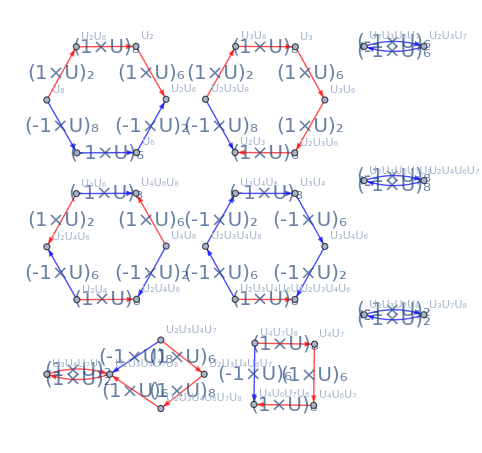

```mathematica
orderOfExpression[getExpression[195]]
e=simplifyExpressionRandomly[getExpression[195],300000]
drawGraph[e]
```